```mathematica
(* Setup *)
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogPlot,LogPlot,LogLinearPlot,ParametricPlot,ParametricPlot3D,SmoothHistogram},PlotStyle->ColorData[45,"ColorList"]];
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogPlot,LogPlot,LogLinearPlot,SmoothHistogram},FillingStyle->Directive[RGBColor[0.5,0.4,0.1]]];
SetOptions[{Plot,ListPlot,ListLinePlot,Plot3D,ListPlot3D,LogPlot,LogLinearPlot,ListLogPlot,ParametricPlot,ParametricPlot3D,TradingChart,CandlestickChart,SmoothHistogram},AxesStyle->Directive[GrayLevel[0.75],FontSize->11,FontFamily->"Ubuntu Mono"]];
SetOptions[{TradingChart,CandlestickChart},TrendStyle->{RGBColor[0,0.8,0],RGBColor[1,0.1,0]},FrameTicksStyle->Directive[GrayLevel[0.75],Dashed,FontSize->10,FontFamily->"Ubuntu Mono"],GridLinesStyle->Directive[GrayLevel[0.5],Dashed]];
```

## Mutual Information

```mathematica
Discretize[val_] := If[Chop[val] == 0, 0, Ceiling[val] ]
FrequencyPad[one_, two_]:= Module[{hash1, hash2, intersect},
hash1=Hash[#1[[1]]]->#1&/@one;
hash2=Hash[#1[[1]]]->#1&/@two;
intersect= hash1[[;;,1]]~Intersection~hash2[[;;,1]];
Return[{intersect/.hash1, intersect/.hash2}];
];
MutualInformation[features_, featurelabels_, col_]:=Module[{yprob,xprob,xyprob1, xyprob0,i},
(*yprob = p(y), xprob = p(x), xyprob1 = p(x|y=1), xyprob0= p(x|y=0) *)
yprob = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[Gather[featurelabels[[;;]] ] ];
xprob = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[Gather[Discretize/@features[[;;, col]] ] ];
xyprob1 = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[
Gather[Select[Transpose[{featurelabels}~Join~{Discretize/@features[[;;,col]]}], #1[[1]]==1&][[;;,2]]]
];
xyprob0 = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[
Gather[Select[Transpose[{featurelabels}~Join~{Discretize/@features[[;;,col]]}], #1[[1]]==0&][[;;,2]]]
];
Return[  yprob[[2,2]] * (xyprob1[[;;,2]].Log@xyprob1[[;;,2]]-#1[[1,;;,2]].Log@#1[[2,;;,2]]&[ FrequencyPad[xyprob1, xprob] ]) +
yprob[[1,2]] * (xyprob0[[;;,2]].Log@xyprob0[[;;,2]]-#1[[1,;;,2]].Log@#1[[2,;;,2]]&[ FrequencyPad[xyprob0, xprob] ])];
];
```

```mathematica
SortBy[#,-#[[2]]&]&@Table[{#3[[c]],N@MutualInformation[#1~Join~#2,ConstantArray[1,Length@#1]~Join~ConstantArray[0,Length@#2],c]},{c,1,Length@#1[[1]]}]&[frdata[[2;;]],dedata[[2;;]],frdata[[1]]]//TableForm
```

flattened_num_nodes | 0.0796473
flattened_num_normal | 0.0636675
num_reverse | 0.0425243
flattened_depth | 0.0413429
depth | 0.0390398
flattened_num_reverse | 0.0371592
mean_height_from_leaf | 0.0336307
flattened_mean_height_from_leaf | 0.0267644
max_depth_reverse | 0.0233554
flattened_max_depth_reverse | 0.0231824
flattened_max_range_reverse | 0.0220475
max_range_reverse | 0.0220475
num_nodes | 0.0212747
num_normal | 0.0198571
flattened_min_range_reverse | 0.0172225
flattened_mean_range_reverse | 0.0171741
mean_range_reverse | 0.0171053
min_range_reverse | 0.0161768
flattened_length | 0.00454451
length | 0.00454451
min_height_tree_from_leaf | 0.00253578
flattened_min_height_tree_from_leaf | 0.00121683

## Logistic Regression

```mathematica
H[X_,θ_,hθ_] := Table[Sum[-X[[i,j]]X[[i,k]]hθ[X[[i]], θ](1-hθ[X[[i]], θ]),{i,1,Length[X]}], {j,1,Length[θ]},{k,1,Length[θ]}]
Delθ[X_,Y_,θ_,hθ_]:=Table[Sum[(Y[[i]]-hθ[X[[i]],θ])X[[i,j]],{i,1,Length[X]}],{j,1,Length[θ]}]
Newton[θ_,X_,Y_,hθ_]:= θ- Inverse[H[X,θ,hθ]].Delθ[X,Y,θ,hθ]
Newton[θ_,{X_,Y_,hθ_}]:= Newton[θ,X,Y,hθ]
```

```mathematica
Iterate[func_,n_,initial_,consts_]:=Module[{temp,i},
temp=initial;
For[i=0,i<n,i++,
 temp =func[temp,consts];
];
Return[temp];
];
```

```mathematica
XX=Table[Join[{1.},#[[i]]],{i,1,Length@#}]&@(hifeatures~Join~frfeatures);YY=ConstantArray[{1.}, Length@hifeatures]~Join~ConstantArray[{0.},Length@frfeatures];
```

```mathematica
Clear[sol]
sol[X_,Y_,θ_]:=Iterate[Newton, 100, θ, {X,Y,1/(1+ⅇ^(-#1.Flatten[#2]))&}]
```

```mathematica
sol[XX,YY,{0.,0.,0.}]
```

```mathematica
Show[
BubbleChart[{Flatten/@Tally@hifeatures,Flatten/@Tally@frfeatures}],
Plot[Solve[0.2542553502946426+-0.34731543843304x1+0.33441826042367423x2==0,x2][[1,1,2]],{x1,0,40},PlotStyle->Thick]
]
```

-Graphics-

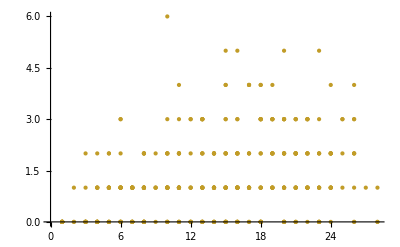

```mathematica
ListPlot@frf[[2;;,{4,5}]]
```

```mathematica
Norm[{1,1},10]
2^(1/10)
```

2^(1/10)

2^(1/10)

## Density Based Estimation

```mathematica
D[(E^( a b)+E^(a c))^(1/p),a]//FullSimplify
```

((ⅇ^(a b)+ⅇ^(a c))^(-1+1/p) (b ⅇ^(a b)+c ⅇ^(a c)))/p

```mathematica
Clear@denseclassifier
denseclassifier[p_:10,k_:1,w_:0.2]:=With[{mins=Min/@Transpose@#,maxs=Max/@Transpose@#},Show[
ContourPlot[Norm[sigmoid@Exp[-k Norm[{x,y}-#]]&/@#,p]/Length[#]^(1/p),{x,mins[[1]]-(maxs-mins)[[1]]*w,maxs[[1]]+(maxs-mins)[[1]]*w},{y,mins[[2]]-(maxs-mins)[[2]]*w,maxs[[2]]+(maxs-mins)[[2]]*w},PlotLegends->Automatic,PlotRange->All, Contours->Table[0.05i,{i,0,20}]]
]]&;
```

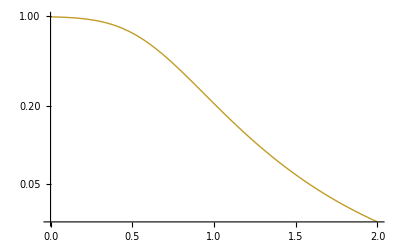

```mathematica
LogPlot[sigmoid[E^(-x)],{x,0,2}]
```

```mathematica
Manipulate[denseclassifier[E^p,k][{{1,1},{3,4}}],{p,0,6},{k,0.1,5}]
```

```mathematica
hif=Import[FileNameJoin[{NotebookDirectory[],"features/english_hindi.csv"}]];
frf=Import[FileNameJoin[{NotebookDirectory[],"features/english_french.csv"}]];
```

```mathematica
Intersection[hif,frf]
```

{{1,1,1,1,0,0,0,0.,0.,1.,0.,1,0,1,1,1,1,0,0,0,0.,0.,1.,0.,1,0},{2,2,2,2,0,0,0,0.,0.,1.66667,0.,1,0,2,1,1,1,0,0,0,0.,0.,1.,0.,1,0},{3,3,3,3,0,0,0,0.,0.,2.25,1.,1,0,3,1,1,1,0,0,0,0.,0.,1.,0.,1,0},{4,4,4,4,0,0,0,0.,0.,2.8,1.,1,0,4,1,1,1,0,0,0,0.,0.,1.,0.,1,0},{5,5,4,4,1,2,2,2.,0.,3.,1.,1,2,5,4,3,3,1,2,2,2.,0.,2.16667,0.,1,2},{5,5,5,5,0,0,0,0.,0.,3.33333,1.41421,1,0,5,1,1,1,0,0,0,0.,0.,1.,0.,1,0},{13,13,13,13,0,0,0,0.,0.,7.42857,4.,1,0,13,1,1,1,0,0,0,0.,0.,1.,0.,1,0},{length,num_nodes,depth,num_normal,num_reverse,max_range_reverse,min_range_reverse,mean_range_reverse,std_dev_range_reverse,mean_height_from_leaf,std_dev_height_from_leaf,min_height_tree_from_leaf,reverse_max_depth,compressed_length,compressed_num_nodes,compressed_depth,compressed_num_normal,compressed_num_reverse,compressed_max_range_reverse,compressed_min_range_reverse,compressed_mean_range_reverse,compressed_std_dev_range_reverse,compressed_mean_height_from_leaf,compressed_std_dev_height_from_leaf,compressed_min_height_tree_from_leaf,compressed_reverse_max_depth}}

```mathematica
denseclassifier[10,0.5][hif[[2;;,{1,16}]]]
denseclassifier[10,0.5][frf[[2;;,{1,16}]]]
```

-Graphics-

-Graphics-

## Topological Data Analysis

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
clusterorder[dmat_]:=dmat[[ #,#]]&@ClusterFlatten@DirectAgglomerate[#,Linkage->"Ward"]&@dmat
```

```mathematica
dmat = Sqrt@DistanceMatrix@hif[[2;;]];
```

```mathematica
ArrayPlot[clusterorder@dmat,ColorFunction->Function[{z},GrayLevel[z^0.66]]]
```

-Graphics-

```mathematica
Juxt[fs_]:=Table[fs[[i]]@#,{i,1,Length[fs]}]&
```

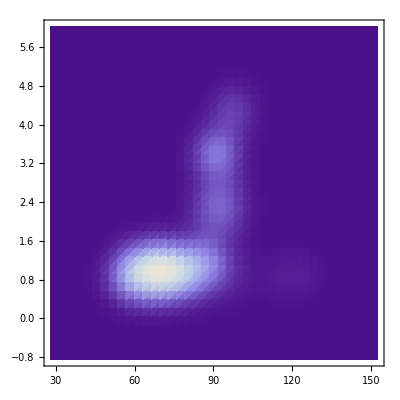

```mathematica
(* This is Cmax (max centrality). You can also use Mean, Geometric Mean, Harmonic Mean, etc *)
centrality[n_,distances_]:=Norm[distances,n] 
density[n_,k_,distances_]:=Norm[Exp[-k #]&/@distances,n]
SmoothDensityHistogram[Juxt[{centrality[10,#]&,density[1,1,#]&}]/@dmat,PlotRange->All]
```

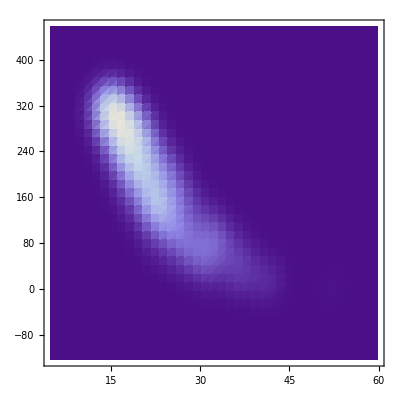
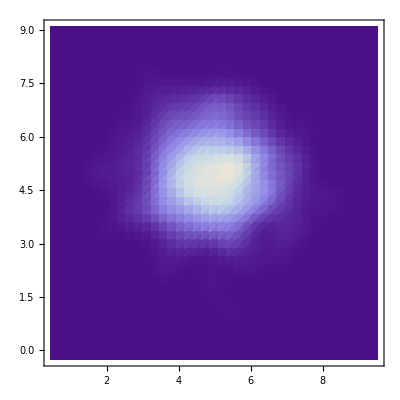

```mathematica
{
SmoothDensityHistogram[Juxt[{centrality[Infinity,#]&,density[1,1,#]&}]/@DistanceMatrix@#,PlotRange->All],
SmoothDensityHistogram[#,PlotRange->All]
}&@RandomVariate[NormalDistribution[5,1],{1000,2}]
```

```mathematica
{u,w,v}=SingularValueDecomposition[hif[[2;;]]]
```

```mathematica
Dimensions[u.w.Transpose[v]]
```

```mathematica
GatherBy[enumerate[Rescale[centrality[Infinity,#]&/@DistanceMatrix@hif[[2;;]]]],Floor[20 #[[2]]]&]
```

{{{1,0.0755397},{5,0.0982222},{10,0.0607184},{28,0.075338},{37,0.0601115},{40,0.0612573},{58,0.0946107},{82,0.068246}},{{2,0.806904},{6,0.806502},{11,0.806904},{13,0.810155},{39,0.846204},{53,0.846204},{56,0.810155},{61,0.810155},{70,0.800048},{75,0.846204}},{{3,0.736949},{4,0.712822},{9,0.736949},{17,0.740264},{36,0.739281},{49,0.73758}},{{7,0.311338},{72,0.322421}},{{8,0.223905},{14,0.239821},{87,0.216339}},{{12,0.109954},{35,0.136736},{47,0.125936},{69,0.149232}},{{15,0.947331},{76,0.947331}},{{16,0.430202},{31,0.442759},{32,0.407763},{65,0.408759},{66,0.414172}},{{18,0.389062},{23,0.395878},{79,0.399934},{85,0.365828}},{{19,0.678545}},{{20,0.51394},{68,0.5229}},{{21,0.977262},{24,0.977262}},{{22,0.285547},{25,0.260918},{41,0.256092},{86,0.257816}},{{26,0.174509},{42,0.164627},{44,0.162693},{57,0.196742},{71,0.154771}},{{27,0.0374817},{30,0.0338667},{55,0.0396294},{59,0.0218102},{60,0.0195835},{83,0.}},{{29,0.881808},{34,0.881808},{43,0.895121},{62,0.895121},{74,0.895121}},{{33,0.755608},{50,0.768587},{80,0.798494}},{{38,0.627864}},{{45,1.},{67,1.},{73,1.},{77,1.},{81,1.}},{{46,0.474914},{48,0.450284},{52,0.495813},{63,0.467619},{64,0.492584},{78,0.480007}},{{51,0.568181},{54,0.591928},{84,0.580369}}}

```mathematica
enumerate[l_]:=MapIndexed[{#2[[1]],#1}&,l]
```